```mathematica
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
(*WARNING!!!!! 0^0=1 in this kernel session, also effects other notebooks!!!!*)

(*foo generates function of efficiency for advanced bell measurements, checked against all combinatorial formulae from fabian with qpc(4,2) and also special cases of steane and surface codes (e.g. Subscript[p, adv]=0 or η=1) have been checked against previous results (of my work) and they agrre*)
foo[data_,trans_,bsm_,numberofqubits_]:=Sum[Sum[(1-trans)^n*trans^(numberofqubits-n)*bsm^(data[[n+1,k,1]])*(1-bsm)^(data[[n+1,k,2]]-data[[n+1,k,1]])*data[[n+1,k,3]],{k,1,Length[data[[n+1]]]}],{n,0,Length[data]-1}]
```

```mathematica
(*Generate the function of efficiencies, the lists for advanced Bell measurements were obtained by 'advanced_bm_plot_data.py'. Only [ and ] needed to be changed to { and }*)
```

```mathematica
golayreasuredata:={1,23,253,1771,8855,33649,100947,244904,486266,786830,1002386,908040,444038,141680,30360,4048,253,0,0,0,0,0,0,0}
```

```mathematica
golayerasure[p_]:=Sum[p^(23-k)(1-p)^k*golayreasuredata[[k+1]],{k,0,23}]
```

```mathematica
(*steane*)
```

```mathematica
steaneznonadvanceddata:={248,1320,1808,896,224,0,0,0}(*['y','z','z','x','x','z','x']*)
```

```mathematica
(*data for steane code+loss+advanced measurements, best results for no-loss*)
steaneadvancedxyz:={{{1,7,10},{2,7,40},{3,7,70},{4,7,70},{5,7,42},{6,7,14},{7,7,2},{0,4,70},{1,4,280},{2,4,420},{3,4,280},{4,4,70},{0,6,10},{1,6,80},{2,6,210},{3,6,280},{4,6,210},{5,6,84},{6,6,14},{0,5,40},{1,5,210},{2,5,420},{3,5,420},{4,5,210},{5,5,42},{0,3,70},{1,3,210},{2,3,210},{3,3,70},{0,2,42},{1,2,84},{2,2,42},{0,1,14},{1,1,14},{0,0,2}},{{1,6,24},{2,6,240},{3,6,464},{4,6,396},{5,6,168},{6,6,28},{0,3,464},{1,3,1584},{2,3,1680},{3,3,560},{0,5,24},{1,5,480},{2,5,1392},{3,5,1584},{4,5,840},{5,5,168},{1,4,1392},{2,4,2376},{3,4,1680},{4,4,420},{0,4,240},{0,2,396},{1,2,840},{2,2,420},{0,1,168},{1,1,168},{0,0,28}},{{1,5,8},{2,5,144},{3,5,816},{4,5,672},{5,5,168},{0,2,816},{1,2,2688},{2,2,1680},{0,4,8},{1,4,288},{2,4,2448},{3,4,2688},{4,4,840},{1,3,2448},{2,3,4032},{3,3,1680},{0,3,144},{1,1,840},{0,0,168},{0,1,672}},{{3,4,448},{4,4,448},{0,1,448},{1,1,1792},{2,3,1344},{3,3,1792},{1,2,1344},{2,2,2688},{0,0,448}},{{3,3,224},{0,0,224},{2,2,672},{1,1,672}}}(*['y','z','z','x','x','z','x']*)
```

```mathematica
steaneadvancedz:={{{3,7,112},{4,7,448},{5,7,336},{6,7,112},{7,7,16},{0,4,112},{1,4,448},{2,4,672},{3,4,448},{4,4,112},{1,3,336},{2,3,336},{3,3,112},{0,0,16}},{{3,6,448},{4,6,1344},{5,6,672},{6,6,112},{0,3,448},{1,3,2688},{2,3,2688},{3,3,896},{1,2,672},{2,2,336},{2,4,1344},{3,4,1344},{4,4,336},{0,0,112}},{{3,5,672},{4,5,1344},{5,5,336},{0,2,672},{1,2,4032},{2,2,2016},{1,1,336},{2,3,4032},{3,3,2016},{2,4,672},{3,4,1344},{4,4,336},{1,3,672},{0,0,336}},{{3,4,448},{4,4,448},{0,1,448},{1,1,1792},{2,2,2688},{1,2,1344},{2,3,1344},{3,3,1792},{0,0,448}},{{3,3,224},{0,0,224},{2,2,672},{1,1,672}}}
```

```mathematica
steaneadvancedxz:={{{1,7,12},{2,7,60},{3,7,124},{4,7,136},{5,7,84},{6,7,28},{7,7,4},{1,5,132},{2,5,336},{3,5,360},{4,5,180},{5,5,36},{1,3,228},{2,3,228},{3,3,76},{0,4,76},{1,4,304},{2,4,456},{3,4,304},{4,4,76},{0,2,36},{1,2,72},{2,2,36},{0,0,4},{0,6,12},{1,6,72},{2,6,180},{3,6,240},{4,6,180},{5,6,72},{6,6,12},{0,5,12},{0,3,72},{0,1,12},{1,1,12}},{{1,6,48},{2,6,192},{3,6,496},{4,6,528},{5,6,240},{6,6,40},{1,4,1104},{2,4,2208},{3,4,1632},{4,4,408},{1,5,384},{2,5,1104},{3,5,1344},{4,5,720},{5,5,144},{1,3,1728},{2,3,1824},{3,3,608},{0,3,496},{0,1,144},{1,1,144},{0,2,336},{1,2,816},{2,2,408},{0,0,40},{0,5,48},{0,4,192}},{{1,5,48},{2,5,192},{3,5,768},{4,5,768},{5,5,192},{1,3,2112},{2,3,4032},{3,3,1728},{1,4,384},{2,4,2112},{3,4,2496},{4,4,768},{0,2,768},{1,2,2880},{2,2,1728},{0,0,192},{0,1,576},{1,1,768},{0,4,48},{0,3,192}},{{3,4,448},{4,4,448},{3,3,1792},{0,1,448},{1,1,1792},{0,0,448},{2,3,1344},{2,2,2688},{1,2,1344}},{{3,3,224},{0,0,224},{2,2,672},{1,1,672}}}
```

```mathematica
(*QPC(n,m), combinatorial results from PRA 95,012327 , this means only ZZ=1 measurements*)
qpcallglin[n_,m_,x_]:=(1-(1-x)^m)^n-(1-(1-x)^m-x^m/2)^n
```

```mathematica
qpcallgnonlin[n_,m_,x_]:=(1-(1-x)^m)^n-(1-(1-x)^m-x^m)^n
```

```mathematica
qpcallglinadv[n_,m_,x_,padv_]:=(1-(1-x)^m)^n-(1-(1-x)^m-(1+padv^m)/2x^m)^n
```

```mathematica
(*QPC(4,2)*)
```

```mathematica
(*linear optics without advanced Bell measurements*)
```

```mathematica
qpc42xyzdata:={496,3328,7680,6144,0,0,0,0,0}(*['y','x','z','z','z','z','z','z']*)
```

```mathematica
(*linear optics with advanced Bell measurements*)
```

```mathematica
qpc42xyzadvanceddata:={{{2,8,256},{3,8,768},{4,8,1120},{5,8,896},{6,8,448},{1,8,32},{7,8,128},{8,8,16},{0,7,32},{1,7,224},{2,7,672},{3,7,1120},{4,7,1120},{5,7,672},{6,7,224},{7,7,32},{0,4,96},{1,4,384},{2,4,576},{3,4,384},{4,4,96},{0,3,96},{1,3,288},{2,3,288},{3,3,96},{0,5,96},{1,5,480},{2,5,960},{3,5,960},{4,5,480},{5,5,96},{0,6,64},{1,6,384},{2,6,960},{3,6,1280},{4,6,960},{5,6,384},{6,6,64},{0,1,32},{1,1,32},{0,2,64},{1,2,128},{2,2,64},{0,0,16}},{{2,7,1248},{3,7,3168},{4,7,4128},{5,7,2976},{1,7,192},{6,7,1056},{7,7,160},{0,6,192},{1,6,1344},{2,6,4128},{3,6,6528},{4,6,5280},{5,6,2112},{6,6,352},{0,4,864},{1,4,3456},{2,4,5184},{3,4,3456},{4,4,864},{0,3,672},{1,3,2208},{2,3,2400},{3,3,864},{0,2,672},{1,2,1344},{2,2,672},{0,5,480},{1,5,2592},{2,5,5568},{3,5,5952},{4,5,3168},{5,5,672},{0,1,288},{1,1,352},{0,0,160}},{{2,6,1920},{3,6,4224},{4,6,5184},{1,6,384},{5,6,3072},{6,6,576},{0,5,384},{1,5,2688},{2,5,7680},{3,5,10752},{4,5,7296},{5,5,1536},{2,4,11136},{1,4,5760},{3,4,9216},{4,4,2496},{0,3,2304},{1,3,7680},{2,3,8448},{3,3,3072},{0,2,2112},{1,2,4608},{2,2,2496},{0,4,1152},{0,1,1152},{1,1,1536},{0,0,576}},{{1,5,256},{2,5,896},{3,5,1920},{4,5,2176},{5,5,896},{0,4,256},{1,4,1792},{2,4,4224},{3,4,5632},{4,4,2944},{1,3,4224},{2,3,6912},{3,3,4352},{0,2,1920},{1,2,5632},{2,2,4352},{0,3,896},{0,1,2176},{1,1,2944},{0,0,896}}}
```

```mathematica
qpc42zadvanceddata:={{{2,8,128},{3,8,768},{4,8,1728},{5,8,1792},{6,8,896},{7,8,256},{8,8,32},{0,6,128},{1,6,768},{2,6,1920},{3,6,2560},{4,6,1920},{5,6,768},{6,6,128},{0,4,192},{1,4,768},{2,4,1152},{3,4,768},{4,4,192},{0,2,128},{1,2,256},{2,2,128},{0,0,32}},{{2,7,768},{3,7,3840},{4,7,6912},{5,7,5376},{6,7,1792},{7,7,256},{0,5,768},{1,5,3840},{2,5,7680},{3,5,7680},{4,5,3840},{5,5,768},{0,4,768},{1,4,3072},{2,4,4608},{3,4,3072},{4,4,768},{0,2,768},{1,2,1536},{2,2,768},{0,3,768},{1,3,2304},{2,3,2304},{3,3,768},{0,1,256},{1,1,256},{0,0,256},{2,6,768},{3,6,3072},{4,6,3840},{5,6,1536},{6,6,256}},{{2,6,1536},{3,6,6144},{4,6,8448},{5,6,4608},{6,6,768},{0,4,1536},{1,4,6144},{2,4,10752},{3,4,9216},{4,4,2304},{0,2,2304},{1,2,4608},{2,2,2304},{0,3,3072},{1,3,9216},{2,3,9216},{3,3,3072},{0,1,1536},{1,1,1536},{0,0,768},{2,5,3072},{3,5,9216},{4,5,7680},{5,5,1536}},{{2,5,1024},{3,5,3072},{4,5,3072},{5,5,1024},{0,3,1024},{1,3,3072},{2,3,6144},{3,3,4096},{0,1,3072},{1,1,3072},{0,2,3072},{1,2,6144},{2,2,4096},{2,4,3072},{3,4,6144},{4,4,3072},{0,0,1024}}}
```

```mathematica
(*surface(3,2)*)
```

```mathematica
surface23[x_]:=x^8+8*x^7*(1-x)+25*x^6*(1-x)^2+(Binomial[8,3]-24)*x^5*(1-x)^3+10*x^4*(1-x)^4
```

```mathematica
(*no advanced Bell measurements*)
```

```mathematica
surface32function[p_,data_]:=Sum[data[[i+1]]*(1-p)^i*p^(8-i),{i,0,8}]
```

```mathematica
surface32zzdata:={400,2624,6096,5152,1024,0,0,0,0}
surface32xyzdata:={508,2732,5072,3568,768,0,0,0,0}


(*advanced Bell measurements*)
surface32zzadvanceddata:={{{2,8,48},{3,8,352},{4,8,896},{5,8,864},{6,8,448},{7,8,128},{8,8,16},{1,5,448},{2,5,1216},{3,5,1280},{4,5,640},{5,5,128},{1,4,416},{2,4,672},{3,4,448},{4,4,112},{0,6,48},{1,6,288},{2,6,720},{3,6,960},{4,6,720},{5,6,288},{6,6,48},{0,5,64},{0,3,128},{1,3,384},{2,3,384},{3,3,128},{0,4,80},{0,2,80},{1,2,160},{2,2,80}},{{3,7,1760},{4,7,3584},{5,7,2592},{2,7,288},{6,7,896},{7,7,128},{1,4,3264},{2,4,6272},{3,4,4352},{4,4,1088},{1,3,3104},{2,3,3264},{3,3,1088},{0,5,288},{1,5,2080},{2,5,5952},{3,5,6592},{4,5,3360},{5,5,672},{0,4,512},{0,2,832},{1,2,1728},{2,2,864},{0,3,832},{0,1,160},{1,1,160},{2,6,320},{3,6,1344},{4,6,1344},{5,6,576},{6,6,96}},{{4,6,4752},{3,6,3072},{5,6,2304},{2,6,624},{6,6,400},{1,3,9344},{2,3,11456},{3,3,3968},{1,2,6336},{2,2,3312},{0,4,624},{1,4,5376},{2,4,14240},{3,4,11072},{4,4,2864},{0,3,1728},{0,1,1152},{1,1,1216},{0,2,2512},{2,5,2880},{3,5,7168},{4,5,4544},{5,5,960},{0,0,80},{1,5,256}},{{3,5,2176},{4,5,2336},{2,5,576},{5,5,576},{1,2,8576},{2,2,5248},{2,3,12224},{3,3,4992},{0,3,576},{1,3,5760},{0,2,2048},{0,1,2080},{1,1,2624},{2,4,5376},{3,4,8064},{4,4,2496},{0,0,448},{1,4,896}},{{2,4,192},{3,4,512},{4,4,320},{1,2,1536},{2,2,1920},{0,2,192},{0,0,320},{2,3,1536},{3,3,1280},{1,3,384},{1,1,1280},{0,1,512}}}
```

```mathematica
(*only xyz=1 measurements and no advanced,('x','z','x','y','z','z','x','z')*)
```

```mathematica
surface32xyzadvanceddata:={{{1,8,14},{2,8,56},{3,8,112},{4,8,140},{5,8,112},{6,8,56},{7,8,16},{8,8,2},{0,6,56},{1,6,336},{2,6,840},{3,6,1120},{4,6,840},{5,6,336},{6,6,56},{0,7,14},{1,7,112},{2,7,336},{3,7,560},{4,7,560},{5,7,336},{6,7,112},{7,7,16},{0,5,112},{1,5,560},{2,5,1120},{3,5,1120},{4,5,560},{5,5,112},{0,4,140},{1,4,560},{2,4,840},{3,4,560},{4,4,140},{0,3,112},{1,3,336},{2,3,336},{3,3,112},{0,2,56},{1,2,112},{2,2,56},{0,1,16},{1,1,16},{0,0,2}},{{2,7,288},{3,7,720},{4,7,872},{5,7,588},{6,7,212},{7,7,32},{1,5,2160},{2,5,5232},{3,5,5880},{4,5,3180},{5,5,672},{1,6,576},{2,6,2160},{3,6,3488},{4,6,2940},{5,6,1272},{6,6,224},{1,4,3488},{2,4,5880},{3,4,4240},{4,4,1120},{1,3,2940},{2,3,3180},{3,3,1120},{0,5,288},{0,3,872},{0,4,720},{0,2,588},{1,2,1272},{2,2,672},{0,1,212},{1,1,224},{0,0,32},{1,7,20},{0,6,20}},{{3,6,1584},{4,6,1904},{5,6,1000},{6,6,200},{2,4,11424},{3,4,10000},{4,4,3000},{2,5,4752},{3,5,7616},{4,5,5000},{5,5,1200},{1,3,7616},{2,3,10000},{3,3,4000},{1,4,4752},{1,2,5000},{2,2,3000},{0,3,1584},{0,1,1000},{1,1,1200},{0,2,1904},{0,0,200},{2,6,384},{1,5,768},{0,4,384}},{{3,5,1216},{4,5,1552},{5,5,512},{2,3,9312},{3,3,5120},{2,4,3648},{3,4,6208},{4,4,2560},{1,2,6208},{2,2,5120},{1,3,3648},{1,1,2560},{0,2,1216},{0,0,512},{0,1,1552},{2,5,288},{1,4,576},{0,3,288}},{{3,4,352},{4,4,320},{3,3,1280},{2,3,1056},{2,2,1920},{1,2,1056},{1,1,1280},{0,1,352},{0,0,320},{2,4,96},{1,3,192},{0,2,96}}}
```

```mathematica
(*Plots*)
```

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedxyz,x,0,7],1/256 foo[steaneadvancedxz,x,0,7],1/256 foo[steaneadvancedz,x,0,7],x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane code with best xyz formation","steane code with best xz formation","steane code with only ZZ=1 measurements","direct transmission"}]]
```

-Graphics-

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedxyz,x,1-2^{-1},7],1/256 foo[steaneadvancedxz,x,1-2^{-1},7],1/256 foo[steaneadvancedz,x,1-2^{-1},7],x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane code with best xyz formation","steane code with best xz formation","steane code with only ZZ=1 measurements","direct transmission"}]]
```

-Graphics-

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedxyz,x,1-2^{-2},7],1/256 foo[steaneadvancedxz,x,1-2^{-2},7],1/256 foo[steaneadvancedz,x,1-2^{-2},7],x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane code with best xyz formation","steane code with best xz formation","steane code with only ZZ=1 measurements","direct transmission"}]]
```

-Graphics-

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedxyz,x,1,7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-7},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-6},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-5},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-4},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-3},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-2},7]/x,1/256 foo[steaneadvancedxyz,x,1-2^{-1},7]/x,1},{x,0.5,1},PlotLegends->{"perfect Bell measurement","v=7","v=6","v=5","v=4","v=3","v=2","v=1"},AxesLabel->{"η",Subscript[η,logical]}]]
```

-Graphics-

```mathematica
(*nonlinear optics allowed*)
```

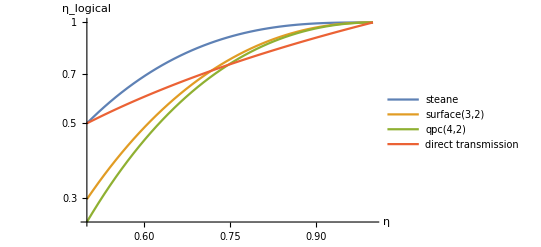

```mathematica
LogPlot[{1/256 foo[steaneadvancedxyz,x,1,7],surface23[x],qpcallgnonlin[4,2,x],x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane","surface(3,2)","qpc(4,2)","direct transmission"}]
```

```mathematica
(*linear optics only standard bm(ZZ=1)*)
```

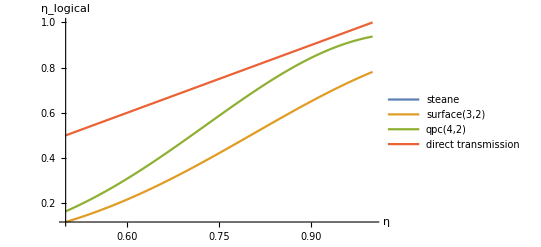

```mathematica
Plot[{1/256 foo[steaneadvancedz,x,0],1/512surface32function[x,surface32zzdata],qpcallglin[4,2,x],x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane","surface(3,2)","qpc(4,2)","direct transmission"}]
```

```mathematica
(*linear optics allowing xyz=1 measurements, no advanced*)
```

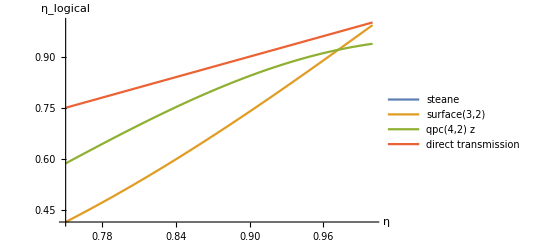

```mathematica
Plot[{1/256 foo[steaneadvancedxyz,x,0],1/512surface32function[x,surface32xyzdata],qpcallglin[4,2,x],x},{x,0.75,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"steane","surface(3,2)","qpc(4,2) z","direct transmission"}]
```

```mathematica
(*surface(3,2) Subscript[p, adv]=0.5*)
```

```mathematica
Plot[{(1/512 foo[surface32xyzadvanceddata,x,1-2^-1,8]),(1/512 foo[surface32zzadvanceddata,x,1-2^-1,8]),x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"surface xyz","surface z","direct transmission"}]
```

```mathematica
(*surface(3,2) Subscript[p, adv]=0*)
```

```mathematica
Plot[{(1/512 foo[surface32xyzadvanceddata,x,0,8]),(1/512 foo[surface32zzadvanceddata,x,0,8]),x},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"surface xyz","surface z","direct transmission"}]
```

```mathematica
(*qpc(4,2) Subscript[p, adv]=0.5*)
```

```mathematica
Plot[{qpcallglinadv[4,2,x,1-2^-1],1/512 foo[qpc42xyzadvanceddata,x,1-2^-1,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotLegends->{"qpc(4,2)","qpc xyz","direct transmission"}]
```

```mathematica
(*comparision of different codes and formations, Subscript[p, adv]=0*)
```

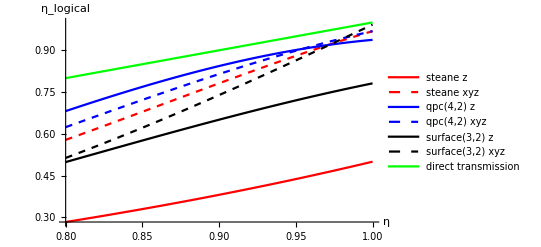

```mathematica
Plot[{1/256 foo[steaneadvancedz,x,0,7],1/256 foo[steaneadvancedxyz,x,0,7],qpcallglinadv[4,2,x,0],1/512 foo[qpc42xyzadvanceddata,x,0,8],1/512 foo[surface32zzadvanceddata,x,0,8],1/512 foo[surface32xyzadvanceddata,x,0,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},PlotLegends->{"steane z","steane xyz","qpc(4,2) z","qpc(4,2) xyz","surface(3,2) z","surface(3,2) xyz","direct transmission"}]
```

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedz,x,0,7],1/256 foo[steaneadvancedxyz,x,0,7],qpcallglinadv[4,2,x,0],1/512 foo[qpc42xyzadvanceddata,x,0,8],1/512 foo[surface32zzadvanceddata,x,0,8],1/512 foo[surface32xyzadvanceddata,x,0,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->14]]
```

```mathematica
Rasterize[LogPlot[{1-1/256 foo[steaneadvancedz,x,1-2^-0,7],1-1/256 foo[steaneadvancedxyz,x,1-2^-0,7],1-qpcallglinadv[4,2,x,1-2^-0],1-1/512 foo[qpc42xyzadvanceddata,x,1-2^-0,8],1-1/512 foo[surface32zzadvanceddata,x,1-2^-0,8],1-1/512 foo[surface32xyzadvanceddata,x,1-2^-0,8],1-x},{x,0.95,1},AxesLabel->{"η",1-Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->22],RasterSize->1500]




(*comparision of different codes and formations, Subscript[p, adv]=0.5*)
```

-Graphics-

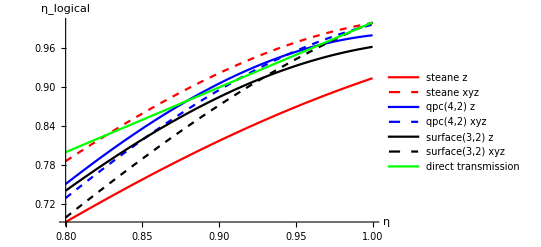

```mathematica
Plot[{1/256 foo[steaneadvancedz,x,1-2^-1,7],1/256 foo[steaneadvancedxyz,x,1-2^-1,7],qpcallglinadv[4,2,x,1-2^-1],1/512 foo[qpc42xyzadvanceddata,x,1-2^-1,8],1/512 foo[surface32zzadvanceddata,x,1-2^-1,8],1/512 foo[surface32xyzadvanceddata,x,1-2^-1,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},PlotLegends->{"steane z","steane xyz","qpc(4,2) z","qpc(4,2) xyz","surface(3,2) z","surface(3,2) xyz","direct transmission"}]
```

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedz,x,1-2^-1,7],1/256 foo[steaneadvancedxyz,x,1-2^-1,7],qpcallglinadv[4,2,x,1-2^-1],1/512 foo[qpc42xyzadvanceddata,x,1-2^-1,8],1/512 foo[surface32zzadvanceddata,x,1-2^-1,8],1/512 foo[surface32xyzadvanceddata,x,1-2^-1,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->14],RasterSize->1500]
```

```mathematica
Rasterize[LogPlot[{1-1/256 foo[steaneadvancedz,x,1-2^-1,7],1-1/256 foo[steaneadvancedxyz,x,1-2^-1,7],1-qpcallglinadv[4,2,x,1-2^-1],1-1/512 foo[qpc42xyzadvanceddata,x,1-2^-1,8],1-1/512 foo[surface32zzadvanceddata,x,1-2^-1,8],1-1/512 foo[surface32xyzadvanceddata,x,1-2^-1,8],1-x},{x,0.95,1},AxesLabel->{"η",1-Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->22],RasterSize->1500]
```

-Graphics-

```mathematica
(*comparision of different codes and formations, Subscript[p, adv]=0.75*)
```

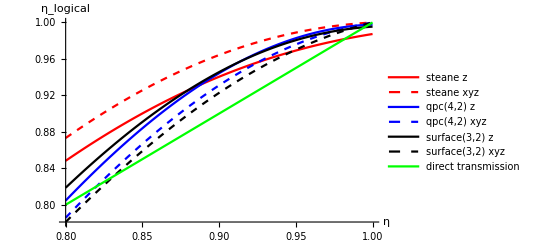

```mathematica
Plot[{1/256 foo[steaneadvancedz,x,1-2^-2,7],1/256 foo[steaneadvancedxyz,x,1-2^-2,7],qpcallglinadv[4,2,x,1-2^-2],1/512 foo[qpc42xyzadvanceddata,x,1-2^-2,8],1/512 foo[surface32zzadvanceddata,x,1-2^-2,8],1/512 foo[surface32xyzadvanceddata,x,1-2^-2,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},PlotLegends->{"steane z","steane xyz","qpc(4,2) z","qpc(4,2) xyz","surface(3,2) z","surface(3,2) xyz","direct transmission"}]
```

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedz,x,1-2^-2,7],1/256 foo[steaneadvancedxyz,x,1-2^-2,7],qpcallglinadv[4,2,x,1-2^-2],1/512 foo[qpc42xyzadvanceddata,x,1-2^-2,8],1/512 foo[surface32zzadvanceddata,x,1-2^-2,8],1/512 foo[surface32xyzadvanceddata,x,1-2^-2,8],x},{x,0.8,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->14],RasterSize->1500]
```

```mathematica
Rasterize[LogPlot[{1-1/256 foo[steaneadvancedz,x,1-2^-2,7],1-1/256 foo[steaneadvancedxyz,x,1-2^-2,7],1-qpcallglinadv[4,2,x,1-2^-2],1-1/512 foo[qpc42xyzadvanceddata,x,1-2^-2,8],1-1/512 foo[surface32zzadvanceddata,x,1-2^-2,8],1-1/512 foo[surface32xyzadvanceddata,x,1-2^-2,8],1-x},{x,0.95,1},AxesLabel->{"η",1-Subscript[η,logical]},PlotStyle->{Red,{Dashed,Red},Blue, {Dashed ,Blue},Black,{Dashed,Black},Green},LabelStyle->FontSize->22],RasterSize->1500]
```

-Graphics-

```mathematica
(*ideal bm*)
```

```mathematica
Rasterize[Plot[{1/256 foo[steaneadvancedz,x,1,7],qpcallglinadv[4,2,x,1],1/512 foo[surface32xyzadvanceddata,x,1,8],x,golayerasure[x]},{x,0.5,1},AxesLabel->{"η",Subscript[η,logical]},PlotStyle->{Red,Blue,Black,Green,Yellow},LabelStyle->FontSize->14],RasterSize->1500]
```

```mathematica
Rasterize[LogPlot[{1-1/256 foo[steaneadvancedz,x,1,7],1-qpcallglinadv[4,2,x,1],1-1/512 foo[surface32xyzadvanceddata,x,1,8],1-x,1-golayerasure[x]},{x,0.8,1},AxesLabel->{"η",1-Subscript[η,logical]},PlotStyle->{Red,Blue,Black,Green,Yellow},LabelStyle->FontSize->22],RasterSize->1500]
```

-Graphics-

```mathematica
(*Table of needed repeater station for outperforming direct transmissionen/PLOB...*)

numberofrepeaterstations2[gain_,improvementfactor_,startn_]:=FindRoot[gain^(n)==(improvementfactor),{n,startn}]

numberofrepeaterstations[gain_,improvementfactor_,startn_]:=FindRoot[gain^(n)==(n*improvementfactor),{n,startn}](*when considering that the teleportion is a process acting on three modes (2 new one and one old), the rhs should read n*improvementfactor(1+1/(2n)) .However this effect is very small*)
(*gain is the ratio between logical transmission efficiency and physical transmission efficiency of the used repeater spacing.
 improvementfactor gives the disired imporvement of the logical transmission in comparision to a single physical transmissio. Therefore the used rescources of the logical tranmission should be considered in this parameter for a fair comparision.
startn is the starting point of the numerical method*)
```

```mathematica
(*calculate the optimal gain for the steane code*)
```

```mathematica
Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}]
```

```mathematica
(*needed number of repeater stations in order to outperform direct transmission(Griece scheme)*)
```

```mathematica
Table[numberofrepeaterstations[Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}][[k,1]],7*2^(k+1),450],{k,1,7}]
```

```mathematica
(*best repeater spacings assuming Subscript[L, att]=22km*)
```

```mathematica
-22Log[{0.9135974818647944,0.8166237871931601,0.7651983319874207,0.7406528955274011,0.7288701948807774,0.7231179797858359,0.7202782080052379}]
```

```mathematica
(*needed number of repeater stations in order to outperform PLOB (assuming a secret key fraction of 1 and using the approximation PLob =1.44η for η<<1 ),(Griece scheme)*)
```

```mathematica
Table[numberofrepeaterstations[Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}][[k,1]],2*1.44*7*2^(k+1),400],{k,1,7}]
```

```mathematica
(*outperform direct transmission, Ewert scheme*)
Table[numberofrepeaterstations[Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}][[k,1]],7*(2^(k+2)-2),450],{k,1,7}]
```

```mathematica
(*outperform PLOB, Ewert scheme*)
Table[numberofrepeaterstations[Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}][[k,1]],2*1.44*7*(2^(k+2)-2),450],{k,1,7}]
```

```mathematica
(*overcoming PLOB, independent of scheme*)
```

```mathematica
Table[numberofrepeaterstations2[Table[FindMaximum[1/256 foo[steaneadvancedxyz,x,1-2^-v,7]/x,{x,1}],{v,1,7}][[k,1]],2*1.44*7,400],{k,1,7}]
```

{{n→122.167},{n→33.9925},{n→22.1899},{n→18.4432},{n→16.9153},{n→16.2222},{n→15.8917}}